```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/shi/file/git/Moat-meanfield/MF_DR/friedel/Riemann

## MS bar

## equations μ=400 MeV

```mathematica
Nc=3;
h=65/10;

ν=482^2;
λ=758/10;

mq0=300.;
(*mq0=20.216128183;*)
ρ0=(2 mq0^2)/h^2;
mPi2=-ν + λ ρ;
mq2=1/2 h^2 ρ;
PiPiVacRen1[p_,ρ_,Λ_]=-(h^2 Nc)/(8 π^2)(mq2(1/2+Log[mq2/Λ^2])+1/2 p^2(-2+Log[mq2/Λ^2]+(√(p^2+4 mq2))/p Log[(√(p^2+4 mq2)+p)/(√(p^2+4 mq2)-p)]));
SigmaPiVacRen[p_,ρ_,Λ_]=p^2+mPi2+PiPiVacRen1[p,ρ,Λ]-(PiPiVacRen1[p,ρ0,Λ]-PiPiVacRen1p0[ρ0,Λ])//Simplify;
pF=√(μ^2-mq2);
PiPiMed[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[Abs[(p+2 pF)/(p-2pF)]]-Log[(pF+μ)^2/mq2]+(√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]));
MSbar1[p_,ρ_,Λ_,μ_]=PiPiVacRen1[p,ρ,Λ]+PiPiMed[p,ρ,μ]+p^2+mPi2//Simplify;
```

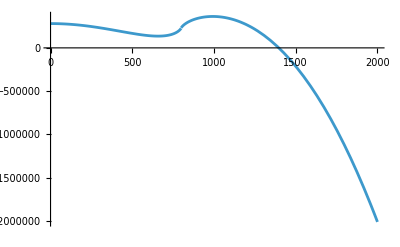

```mathematica
Plot[MSbar1[p,19.346359230155954,300.,400.],{p,0,2000}]
```

### First Riemann sheet

```mathematica
plot1=Show[ComplexPlot3D[MSbar1[p,19.346359230155954,300.,400.],{p,-1000-ⅈ 1000,1000+ⅈ 1000},ViewPoint->{1.,-1.,1},ViewVertical->{0,0,1},
AxesLabel->{Style["Re[p] [MeV]",20,FontFamily->"Times",Black],Style["Im[p] [MeV]",20,FontFamily->"Times",Black],Rotate[Style["Σ_π(p) [MeV^2] ",20,FontFamily->"Times",Black],π/2]},TicksStyle->Directive[FontSize->14,FontFamily->"Times",Bold](*,PlotLabel->Style["OverBar[MS]",30,FontFamily->"Times",Black]*),ImageSize->700,ImagePadding->{{90,10},{10,10}}],Graphics3D[{Text[Style["Sheet 1",20,Bold,Black],{-1000,0,0.8 10^6}  ]}],Graphics3D[{Text[Style["μ=400 MeV",25,Black],{-1000,0,1.2 10^6}  ]}]]
```

-Graphics3D-

```mathematica
Export["./Riemannsheet1MSbarmu400.pdf",plot1]
```

./Riemannsheet1MSbarmu400.pdf

### Second Riemann sheet of sqart

```mathematica
PiPiMed2[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[Abs[(p+2 pF)/(p-2pF)]]-Log[(pF+μ)^2/mq2]+(-√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]));
MSbar2[p_,ρ_,Λ_,μ_]=PiPiVacRen1[p,ρ,Λ]+PiPiMed2[p,ρ,μ]+p^2+mPi2//Simplify;
```

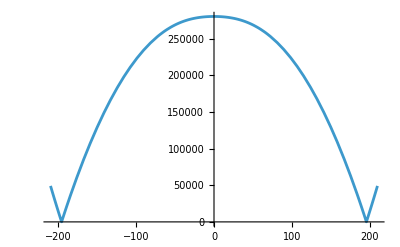

```mathematica
Plot[Abs[MSbar2[p,19.346359230155954,300.,400.]],{p,-210,210}]
```

```mathematica
√((19.346359230155954 6.5^2)/2)
```

20.2161

```mathematica
mq2=20.21612818363211^2;
```

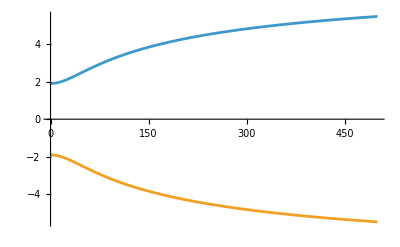

```mathematica
Plot[{(√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]/.{pF->√(μ^2-mq2)}/.{mq2->20.216^2,μ->400},(-√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]/.{pF->√(μ^2-mq2)}/.{mq2->20.216^2,μ->400}},{p,0,500}]
```

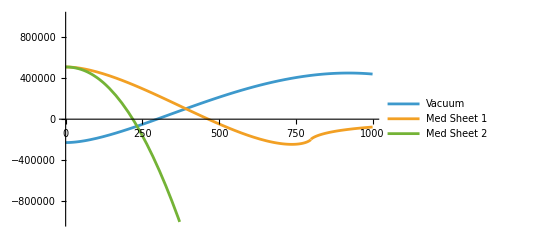

```mathematica
Plot[{PiPiVacRen1[p,19.346359230155954,300]+p^2+mPi2/.{ρ->19.346359230155954},PiPiMed[p,19.346359230155954,400],PiPiMed2[p,19.346359230155954,400]},{p,0,1000},PlotRange->{All,{-10^6,10^6}},PlotLegends->{"Vacuum","Med Sheet 1","Med Sheet 2"}]
```

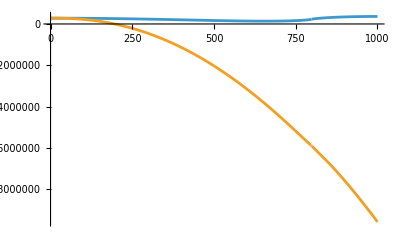

```mathematica
Plot[{MSbar1[p,19.346359230155954,300.,400.],MSbar2[p,19.346359230155954,300.,400.]},{p,0,1000}]
```

```mathematica
plot1=Show[ComplexPlot3D[MSbar2[p,19.346359230155954,300.,400.],{p,-1000-ⅈ 1000,1000+ⅈ 1000},ViewPoint->{1.,-1.,1.},ViewVertical->{0,0,1},
AxesLabel->{Style["Re[p] [MeV]",20,FontFamily->"Times",Black],Style["Im[p] [MeV]",20,FontFamily->"Times",Black],Rotate[Style["Σ_π(p) [MeV^2]",20,FontFamily->"Times",Black],π/2]},TicksStyle->Directive[FontSize->14,FontFamily->"Times",Bold],ImageSize->700,ImagePadding->{{90,10},{10,10}}],Graphics3D[{Text[Style["Sheet 2",20,Bold,Black],{-1000,0,1.7 10^7}  ]}]]
```

-Graphics3D-

```mathematica
Export["./Riemannsheet2MSbarmu400.pdf",plot1]
```

./Riemannsheet2MSbarmu400.pdf

### Second Riemann sheet of Log

```mathematica
PiPiMed3[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[Abs[(p+2 pF)/(p-2pF)]]-Log[(pF+μ)^2/mq2]+(√(p^2+4 mq2))/p (Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]+ⅈ 2π)));
MSbar3[p_,ρ_,Λ_,μ_]=PiPiVacRen1[p,ρ,Λ]+PiPiMed3[p,ρ,μ]+p^2+mPi2//Simplify;
```

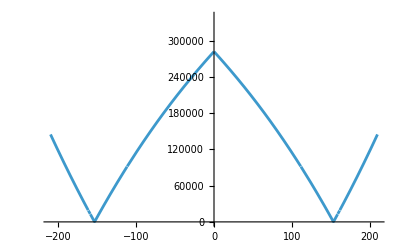

```mathematica
Plot[Abs[MSbar3[p+ⅈ 164,19.346359230155954,300.,400.]],{p,-210,210},PlotRange->{All,{0,340000}}]
```

```mathematica
plot1=Show[ComplexPlot3D[MSbar3[p,19.346359230155954,300.,400.],{p,-1000-ⅈ 1000,1000+ⅈ 1000},ViewPoint->{1.,-1.,1.},ViewVertical->{0,0,1},
AxesLabel->{Style["Re[p] [MeV]",20,FontFamily->"Times",Black],Style["Im[p] [MeV]",20,FontFamily->"Times",Black],Rotate[Style["Σ_π(p) [MeV^2]",20,FontFamily->"Times",Black],π/2]},TicksStyle->Directive[FontSize->14,FontFamily->"Times",Bold],ImageSize->700,ImagePadding->{{90,10},{10,10}}],Graphics3D[{Text[Style["Sheet 3",20,Bold,Black],{-1000,0,8 10^6}  ]}]]
```

-Graphics3D-

```mathematica
Export["./Riemannsheet3MSbarmu400.pdf",plot1]
```

./Riemannsheet3MSbarmu400.pdf

## equations μ=301 MeV

```mathematica
Nc=3;
h=65/10;

ν=482^2;
λ=758/10;

mq0=300;
(*mq0=20.216128183;*)
ρ0=(2 mq0^2)/h^2;
mPi2=-ν + λ ρ;
mq2=1/2 h^2 ρ;
PiPiVacRen1[p_,ρ_,Λ_]=-(h^2 Nc)/(8 π^2)(mq2(1/2+Log[mq2/Λ^2])+1/2 p^2(-2+Log[mq2/Λ^2]+(√(p^2+4 mq2))/p Log[(√(p^2+4 mq2)+p)/(√(p^2+4 mq2)-p)]));
SigmaPiVacRen[p_,ρ_,Λ_]=p^2+mPi2+PiPiVacRen1[p,ρ,Λ]-(PiPiVacRen1[p,ρ0,Λ]-PiPiVacRen1p0[ρ0,Λ])//Simplify;
pF=√(μ^2-mq2);
PiPiMed[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[Abs[(p+2 pF)/(p-2pF)]]-Log[(pF+μ)^2/mq2]+(√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]));
MSbar1[p_,ρ_,Λ_,μ_]=PiPiVacRen1[p,ρ,Λ]+PiPiMed[p,ρ,μ]+p^2+mPi2//Simplify;
```

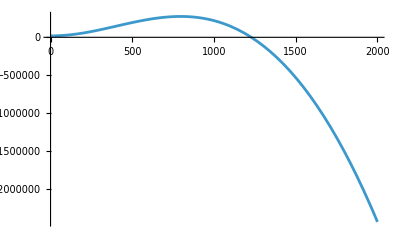

```mathematica
Plot[MSbar1[p,4283.491034268094,300.,301.],{p,0,2000}]
```

### First Riemann sheet

```mathematica
plot1=Show[ComplexPlot3D[MSbar1[p,4283.491034268094,300.,301.],{p,-1000-ⅈ 1000,1000+ⅈ 1000},ViewPoint->{1.,-1.,1.1},ViewVertical->{0,0,1},
AxesLabel->{Style["Re[p] [MeV]",20,FontFamily->"Times",Black],Style["Im[p] [MeV]",20,FontFamily->"Times",Black],Rotate[Style["Σ_π(p) [MeV^2] ",20,FontFamily->"Times",Black],π/2]},TicksStyle->Directive[FontSize->14,FontFamily->"Times",Bold],PlotLabel->Style["1                                OverBar[MS]                                 ",30,FontFamily->"Times",Black],ImageSize->700,ImagePadding->{{90,10},{10,10}}],Graphics3D[{Text[Style["μ=301 MeV",25,Black],{-1000,0,1.7 10^6}  ]}],Graphics3D[{Text[Style["Sheet 1",20,Bold,Black],{-1000,0,1.1 10^6}  ]}]]
```

-Graphics3D-

```mathematica
Export["./Riemannsheet1MSbarmu301.pdf",plot1]
```

./Riemannsheet1MSbarmu301.pdf

### Second Riemann sheet of sqart

```mathematica
PiPiMed2[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[Abs[(p+2 pF)/(p-2pF)]]-Log[(pF+μ)^2/mq2]+(-√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]));
MSbar2[p_,ρ_,Λ_,μ_]=PiPiVacRen1[p,ρ,Λ]+PiPiMed2[p,ρ,μ]+p^2+mPi2//Simplify;
```

```mathematica
Plot[{(√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))],(-√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]}/.{pF->√(μ^2-mq2)}/.{mq2->300.^2,μ->301},{p,0,500}]
```

-Graphics-

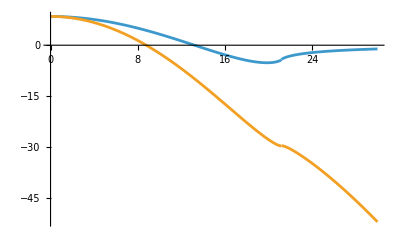

```mathematica
Plot[{(*PiPiVacRen1[p,4283.491034268094,300]+p^2+mPi2/.{ρ->4283.491034268094},*)PiPiMed[p,4283.491034268094,301],PiPiMed2[p,4283.491034268094,301]},{p,0,30}]
```

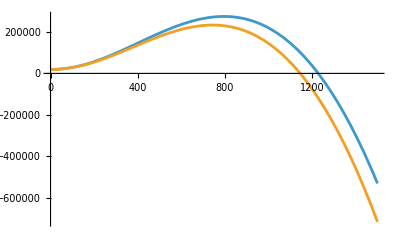

```mathematica
Plot[{MSbar1[p,4283.491034268094,300.,301],MSbar2[p,4283.491034268094,300.,301]},{p,0,1500}]
```

```mathematica
plot1=Show[ComplexPlot3D[MSbar2[p,4283.491034268094,300.,301.],{p,-1000-ⅈ 1000,1000+ⅈ 1000},ViewPoint->{1.,-1.,1},ViewVertical->{0,0,1},
AxesLabel->{Style["Re[p] [MeV]",20,FontFamily->"Times",Black],Style["Im[p] [MeV]",20,FontFamily->"Times",Black],Rotate[Style["Σ_π(p) [MeV^2]",20,FontFamily->"Times",Black],π/2]},TicksStyle->Directive[FontSize->14,FontFamily->"Times",Bold],PlotLabel->Style["3                                                                       ",30,FontFamily->"Times",Black],ImageSize->700,ImagePadding->{{90,10},{10,10}}],Graphics3D[{Text[Style["μ=301 MeV",25,Black],{-1000,0,1.7 10^6}  ]}],Graphics3D[{Text[Style["Sheet 2",20,Bold,Black],{-1000,0,1.1 10^6}  ]}]]
```

-Graphics3D-

```mathematica
Export["./Riemannsheet2MSbarmu301.pdf",plot1]
```

./Riemannsheet2MSbarmu301.pdf

### Second Riemann sheet of Log

```mathematica
PiPiMed3[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[Abs[(p+2 pF)/(p-2pF)]]-Log[(pF+μ)^2/mq2]+(√(p^2+4 mq2))/p (Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]+ⅈ 2π)));
MSbar3[p_,ρ_,Λ_,μ_]=PiPiVacRen1[p,ρ,Λ]+PiPiMed3[p,ρ,μ]+p^2+mPi2//Simplify;
```

```mathematica
plot1=Show[ComplexPlot3D[MSbar3[p,4283.491034268094,300.,301.],{p,-1000-ⅈ 1000,1000+ⅈ 1000},ViewPoint->{1.,-1.,1.1},ViewVertical->{0,0,1},
AxesLabel->{Style["Re[p] [MeV]",20,FontFamily->"Times",Black],Style["Im[p] [MeV]",20,FontFamily->"Times",Black],Rotate[Style["Σ_π(p) [MeV^2]",20,FontFamily->"Times",Black],π/2]},TicksStyle->Directive[FontSize->14,FontFamily->"Times",Bold],ImageSize->700,ImagePadding->{{90,10},{10,10}}],Graphics3D[{Text[Style["Sheet 3",20,Bold,Black],{-1000,0,9 10^6}  ]}]]
```

-Graphics3D-

```mathematica
Export["./Riemannsheet3MSbarmu301.pdf",plot1]
```

./Riemannsheet3MSbarmu301.pdf

## MS bar Vacuum subtraction

## equations μ=400 MeV

```mathematica
Nc=3;
h=65/10;
ν=482^2;
λ=758/10;
mq0=300.;
(*mq0=20.216128183;*)
ρ0=(2 mq0^2)/h^2;
mPi2=-ν + λ ρ;
mq2=1/2 h^2 ρ;
PiPiVacRen1[p_,ρ_,Λ_]=-(h^2 Nc)/(8 π^2)(mq2(1/2+Log[mq2/Λ^2])+1/2 p^2(-2+Log[mq2/Λ^2]+(√(p^2+4 mq2))/p Log[(√(p^2+4 mq2)+p)/(√(p^2+4 mq2)-p)]));
PiPiVacRen1p0[ρ_,Λ_]=Limit[PiPiVacRen1[p,ρ1,Λ],p->0]/.{ρ1->ρ};
SigmaPiVacRen[p_,ρ_,Λ_]=p^2+mPi2+PiPiVacRen1[p,ρ,Λ]-(PiPiVacRen1[Re[p],ρ0,Λ]-PiPiVacRen1p0[ρ0,Λ])//Simplify;
pF=√(μ^2-mq2);
PiPiMed[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[Abs[(p+2 pF)/(p-2pF)]]-Log[(pF+μ)^2/mq2]+(√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]));
MSbarvac1[p_,ρ_,Λ_,μ_]=SigmaPiVacRen[p,ρ,Λ]+PiPiMed[p,ρ,μ]//Simplify;
```

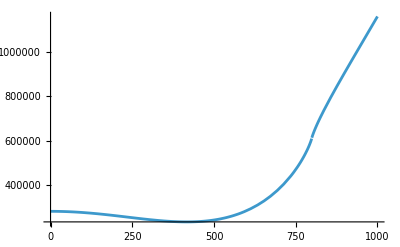

```mathematica
Plot[Re[MSbarvac1[(*200+ⅈ*) p,19.346359230155954,300.,400.]],{p,0,1000},PlotRange->{All,All}]
```

### First Riemann sheet

```mathematica
plot1=Show[ComplexPlot3D[MSbarvac1[p,19.346359230155954,300.,400.],{p,-1000-ⅈ 1000,1000+ⅈ 1000},ViewPoint->{1, -1, 1},ViewVertical->{0,0,1},
AxesLabel->{Style["Re[p] [MeV]",20,FontFamily->"Times",Black],Style["Im[p] [MeV]",20,FontFamily->"Times",Black],Rotate[Style["Σ_π(p) [MeV^2] ",20,FontFamily->"Times",Black],π/2]},TicksStyle->Directive[FontSize->14,FontFamily->"Times",Bold],PlotLabel->Style["μ=400 MeV",30,FontFamily->"Times",Black],ImageSize->700,ImagePadding->{{90,10},{10,10}}],Graphics3D[{Text[Style["Sheet 1",20,Bold,Black],{-1000,0,1.5 10^6}  ]}]]
```

-Graphics3D-

```mathematica
Export["./Riemannsheet1MSbarvacmu400.pdf",plot1]
```

./Riemannsheet1MSbarvacmu400.pdf

### Second Riemann sheet of sqart

```mathematica
PiPiMed2[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[Abs[(p+2 pF)/(p-2pF)]]-Log[(pF+μ)^2/mq2]+(-√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]));
MSbarvac2[p_,ρ_,Λ_,μ_]=SigmaPiVacRen[p,ρ,Λ]+PiPiMed2[p,ρ,μ]//Simplify;
```

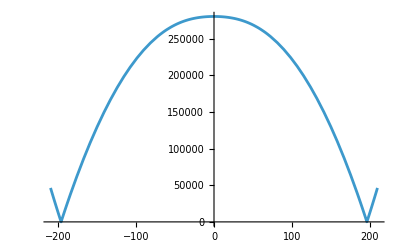

```mathematica
Plot[Abs[MSbarvac2[p,19.346359230155954,300.,400.]],{p,-210,210}]
```

```mathematica
plot1=Show[ComplexPlot3D[MSbarvac2[p,19.346359230155954,300.,400.],{p,-1000-ⅈ 1000,1000+ⅈ 1000},ViewPoint->{1.,-1.,1.1},ViewVertical->{0,0,1},
AxesLabel->{Style["Re[p] [MeV]",20,FontFamily->"Times",Black],Style["Im[p] [MeV]",20,FontFamily->"Times",Black],Rotate[Style[" Σ_π(p) [MeV^2]",20,FontFamily->"Times",Black],π/2]},TicksStyle->Directive[FontSize->14,FontFamily->"Times",Bold],ImageSize->700,ImagePadding->{{90,10},{10,10}}],Graphics3D[{Text[Style["Sheet 2",20,Bold,Black],{-1000,0,1.5 10^7}  ]}]]
```

-Graphics3D-

```mathematica
Export["./Riemannsheet2MSbarvacmu400.pdf",plot1]
```

./Riemannsheet2MSbarvacmu400.pdf

### Second Riemann sheet of Log

```mathematica
PiPiMed3[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[Abs[(p+2 pF)/(p-2pF)]]-Log[(pF+μ)^2/mq2]+(√(p^2+4 mq2))/p (Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]+ⅈ 2π)));
MSbarvac3[p_,ρ_,Λ_,μ_]=SigmaPiVacRen[p,ρ,Λ]+PiPiMed3[p,ρ,μ]//Simplify;
```

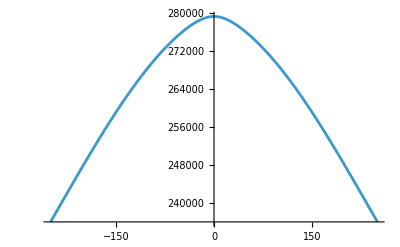

```mathematica
Plot[Re[MSbarvac3[p+ⅈ 2π,19.346359230155954,300.,400.]],{p,-250,250}]
```

```mathematica
plot1=Show[ComplexPlot3D[MSbarvac3[p,19.346359230155954,300.,400.],{p,-1000-ⅈ 1000,1000+ⅈ 1000},ViewPoint->{1.,-1.,0.99},ViewVertical->{0,0,1},
AxesLabel->{Style["Re[p] [MeV]",20,FontFamily->"Times",Black],Style["Im[p] [MeV]",20,FontFamily->"Times",Black],Rotate[Style["Σ_π(p) [MeV^2]",20,FontFamily->"Times",Black],π/2]},TicksStyle->Directive[FontSize->14,FontFamily->"Times",Bold],ImageSize->700,ImagePadding->{{90,10},{10,10}}],Graphics3D[{Text[Style["Sheet 3",20,Bold,Black],{-1000,0,8 10^6}  ]}]]
```

-Graphics3D-

```mathematica
Export["./Riemannsheet3MSbarvacmu400.pdf",plot1]
```

./Riemannsheet3MSbarvacmu400.pdf

## equations μ=301 MeV

```mathematica
Nc=3;
h=65/10;

ν=482^2;
λ=758/10;

mq0=300.;
(*mq0=20.216128183*)
ρ0=(2 mq0^2)/h^2;
mPi2=-ν + λ ρ;
mq2=1/2 h^2 ρ;
PiPiVacRen1[p_,ρ_,Λ_]=-(h^2 Nc)/(8 π^2)(mq2(1/2+Log[mq2/Λ^2])+1/2 p^2(-2+Log[mq2/Λ^2]+(√(p^2+4 mq2))/p Log[(√(p^2+4 mq2)+p)/(√(p^2+4 mq2)-p)]));
PiPiVacRen1p0[ρ_,Λ_]=Limit[PiPiVacRen1[p,ρ1,Λ],p->0]/.{ρ1->ρ};
SigmaPiVacRen[p_,ρ_,Λ_]=p^2+mPi2+PiPiVacRen1[p,ρ,Λ]-(PiPiVacRen1[Re[p],ρ0,Λ]-PiPiVacRen1p0[ρ0,Λ])//Simplify;
pF=√(μ^2-mq2);
PiPiMed[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[Abs[(p+2 pF)/(p-2pF)]]-Log[(pF+μ)^2/mq2]+(√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]));
MSbarvac1[p_,ρ_,Λ_,μ_]=SigmaPiVacRen[p,ρ,Λ]+PiPiMed[p,ρ,μ]//Simplify;
```

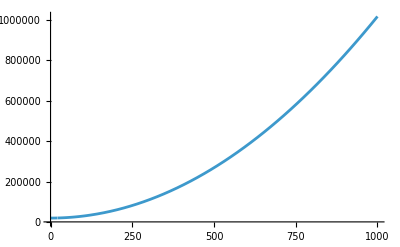

```mathematica
Plot[MSbarvac1[p,4283.491034268094,300.,301.],{p,0,1000}]
```

### First Riemann sheet

```mathematica
plot1=Show[ComplexPlot3D[MSbarvac1[p,4283.491034268094,300.,301.],{p,-1000-ⅈ 1000,1000+ⅈ 1000},ViewPoint->{1, -1, 1},ViewVertical->{0,0,1},
AxesLabel->{Style["Re[p] [MeV]",20,FontFamily->"Times",Black],Style["Im[p] [MeV]",20,FontFamily->"Times",Black],Rotate[Style["Σ_π(p) [MeV^2] ",20,FontFamily->"Times",Black],π/2]},TicksStyle->Directive[FontSize->14,FontFamily->"Times",Bold],PlotLabel->Style["2                              OverBar[MS]+VS                                 ",30,FontFamily->"Times",Black],ImageSize->700,ImagePadding->{{90,10},{10,10}}],Graphics3D[{Text[Style["Sheet 1",20,Bold,Black],{-1000,0,1.8 10^6}  ]}]]
```

-Graphics3D-

```mathematica
Export["./Riemannsheet1MSbarvacmu301.pdf",plot1]
```

./Riemannsheet1MSbarvacmu301.pdf

### Second Riemann sheet of sqart

```mathematica
PiPiMed2[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[Abs[(p+2 pF)/(p-2pF)]]-Log[(pF+μ)^2/mq2]+(-√(p^2+4 mq2))/p Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]));
MSbarvac2[p_,ρ_,Λ_,μ_]=SigmaPiVacRen[p,ρ,Λ]+PiPiMed2[p,ρ,μ]//Simplify;
```

```mathematica
plot1=Show[ComplexPlot3D[MSbarvac2[p,4283.491034268094,300.,301.],{p,-1000-ⅈ 1000,1000+ⅈ 1000},ViewPoint->{1.,-1.,1.1},ViewVertical->{0,0,1},
AxesLabel->{Style["Re[p] [MeV]",20,FontFamily->"Times",Black],Style["Im[p] [MeV]",20,FontFamily->"Times",Black],Rotate[Style[" Σ_π(p) [MeV^2] ",20,FontFamily->"Times",Black],π/2]},TicksStyle->Directive[FontSize->14,FontFamily->"Times",Bold],ImageSize->700,ImagePadding->{{90,10},{10,10}}],Graphics3D[{Text[Style["Sheet 2",20,Bold,Black],{-1000,0,1.5 10^6}  ]}]]
```

-Graphics3D-

```mathematica
Export["./Riemannsheet2MSbarvacmu301.pdf",plot1]
```

./Riemannsheet2MSbarvacmu301.pdf

### Second Riemann sheet of Log

```mathematica
PiPiMed3[p_,ρ_,μ_]=(Nc h^2)/(8 π^2)(2 μ pF+mq2 Log[(μ-pF)/(μ+pF)]+1/2 p^2((√(p^2+4 mq2)-2 μ)/p Log[Abs[(p+2 pF)/(p-2pF)]]-Log[(pF+μ)^2/mq2]+(√(p^2+4 mq2))/p (Log[(2 mq2+p pF+μ √(p^2+4 mq2))/(2 mq2-p pF+μ √(p^2+4 mq2))]+ⅈ 2π)));
MSbarvac3[p_,ρ_,Λ_,μ_]=SigmaPiVacRen[p,ρ,Λ]+PiPiMed3[p,ρ,μ]//Simplify;
```

```mathematica
plot1=Show[ComplexPlot3D[MSbarvac3[p,4283.491034268094,300.,301.],{p,-1000-ⅈ 1000,1000+ⅈ 1000},ViewPoint->{1.,-1.,1},ViewVertical->{0,0,1},
AxesLabel->{Style["Re[p] [MeV]",20,FontFamily->"Times",Black],Style["Im[p] [MeV]",20,FontFamily->"Times",Black],Rotate[Style["Σ_π(p) [MeV^2]",20,FontFamily->"Times",Black],π/2]},TicksStyle->Directive[FontSize->14,FontFamily->"Times",Bold],ImageSize->700,ImagePadding->{{90,10},{10,10}}],Graphics3D[{Text[Style["Sheet 3",20,Bold,Black],{-1000,0,9 10^6}  ]}]]
```

-Graphics3D-

```mathematica
Export["./Riemannsheet3MSbarvacmu301.pdf",plot1]
```

./Riemannsheet3MSbarvacmu301.pdf